```mathematica
λ=500*^-9;
k=(2 π)/λ;
w=1*^-3;
z=100;
min=-0.01;max=0.01;step=400;
d=(max-min)/step;
x=Range[min,max,d];
y=Table[ If[Abs[x]<=w/2,1,0],{x,Range[min,max,d]}];
scale1=λ/(step d);
endx=x scale1;
```

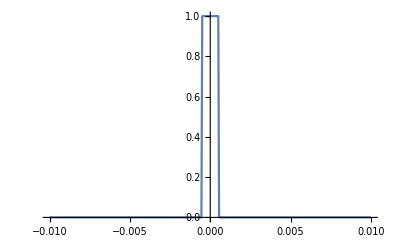

```mathematica
ListLinePlot[y,PlotRange->All,DataRange->{min,max}]
```

```mathematica
h2=Exp[I k z]/(√(I λ z)) Exp[(I k)/(2 z)endx^2];
h1=Exp[(I k)/(2 z) x^2];
yscal=Total[Abs[y h1]^2 d]/Total[Abs[Fourier[(y h1)^2]*(endx[[2]]-endx[[1]])]];
fres1=Fourier[y*h1*(-1)^Table[i,{i,Length[x]}]]*√yscal*h2;
```

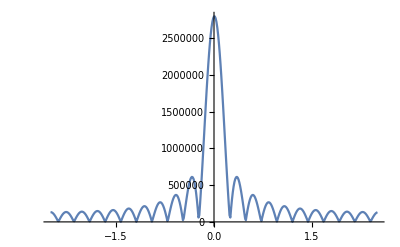

```mathematica
ListLinePlot[Transpose[{endx,Abs[fres1*√yscal]}],PlotRange->All]
```

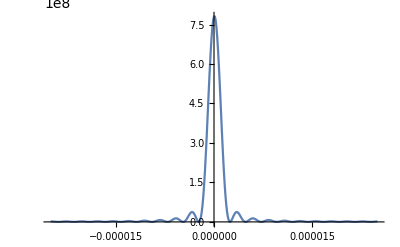

```mathematica
ListLinePlot[Transpose[{endx,Abs[fres1^2*yscal]}],PlotRange->All]
```

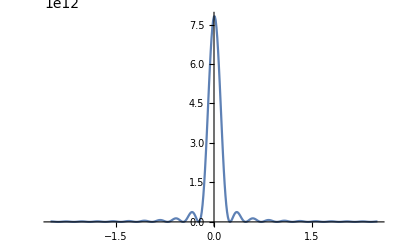

```mathematica
ListLinePlot[Transpose[{endx,Abs[fres1^2*yscal]}],PlotRange->All]
```

```mathematica
angleendx=ArcTan[endx/z];
```

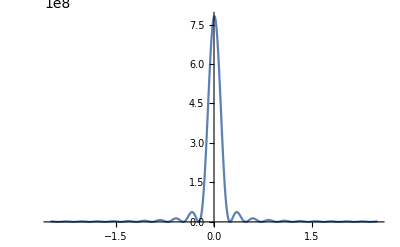

```mathematica
ListLinePlot[Transpose[{angleendx,Abs[fres1^2*yscal]}],PlotRange->All]
```